## Zenbaki errealen serieak eta π zenbakia

### Zirkuluaren koadraturaren problema

Bila ezazu sarean zer den zirkuluaren koadratura.

XIX. mendean, Ferdinand Lindemann matematikari alemaniarrak frogatu zuen π zenbakia transzendentea dela, eta beraz, greziarren zirkuluaren koadraturaren problema ebatzi ezina dela.

### Hurbilpen metodoak: π zenbakiaren hurbilpenak

#### Zirkuluaren koadratura hurbildua: Arkimedes-en metodoa

Arkimedes-en prozedura (K. a. III. mendea)

```mathematica
ArkimedesenZirkuloa[100]
```

#### Leibniz-en formula

1682 urtean, Leibniz matematikari alemaniarrak berdintza hau frogatu zuen:

				π = ∑_(n=0)^∞ (-1)^n/(2n+1) = 4(1-1/3+1/5-1/7+...). 
Baina, guk egokituko dugu n=1 baliotik hasteko.

```mathematica
LeibnizenBatura[k_Integer]:=4 Sum[(-1)^(i+1)/(2i-1),{i,1,k}]
```

Matematikari horren izena daraman irizpidearen arabera, seriea konbergentea da.

Ondoren, serie horren batura partzial bat kalkulatuz, π zenbakiaren hurbilpen bat lortuko dugu:

```mathematica
LeibnizenBatura[1000]//N
```

3.14059

1) Aurrreikus ezazu nolakoa izango den gehienez hurbilpen horren errorea, serie alternatuetarako teorian ikusitakoa erabiliz (eman itzazu erantzunaren azalpenak).

```mathematica
4/(2*1000+1)//N
```

0.001999

| LeibnizenBatura[1000] - π | ≤  a_1000+1 = 0.001999

Ondoren, kalkula ezazu benetan egindako errorearen balio absolutua, eta egiazta ezazu goian kalkulatutako errorearen bornea zuzena den.

```mathematica
Abs[LeibnizenBatura[1000]-π]//N
```

0.001

2) Zenbat batugai batu beharko ditugu errorearen balio absolutua 10^-4 baino txikiagoa izateko?

```mathematica
N[Solve[4/(2h+1)==10^(-4),h]]
```

{{h→19999.5}}

```mathematica
h = 20000
```

20000

3) Batura partzial hori kalkulatu, eta egiaztatu lortu duzun π zenbakiaren hurbilpenaren doitasuna eskatutakoa den.

```mathematica
LeibnizenBatura[h]//N
```

3.14154

```mathematica
Abs[LeibnizenBatura[h]-π]//N
```

0.00005

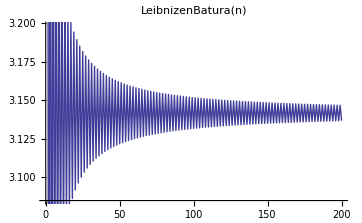

```mathematica
ListPlot[Table[LeibnizenBatura[n],{n,1,200}],Joined->True,PlotLabel->HoldForm[LeibnizenBatura[n]]]
```

4) Leibniz-en seriea erabiliz, lor ezazu 10^-4 baino txikiagoko luzeradun [a,b] tarte bat, π zenbakia barne duena.

```mathematica
N[Solve[4/(2*(2j+1)-1)== 10^(-4),j]]
```

{{j→9999.75}}

```mathematica
j=10000
```

10000

```mathematica
LeibnizenBatura[j]//N
```

3.14149

```mathematica
LeibnizenBatura[j+1]//N
```

3.14169

```mathematica
a = 3.141492653590043
```

```mathematica
b = 3.1416926435905435
```

#### Sharp-en formula

1699an, Abraham Sharp matematikari ingelesak π zenbakiaren 71 zifra zehatz lortu zituen, ondoko formula erabiliz:

			π =2 √3 ∑_(n=1)^∞ (-1/3)^(n-1)/(2n-1) = 2 √3(1-1/(3×3)+1/(5×3^2)-1/(7×3^3)+...).

```mathematica
SharpenBatura[k_Integer]:=2 √3 ∑_(i=1)^k (-1/3)^(i-1)/(2 i-1)
```

5) Sharpek  π zenbakiaren 71 zifra zehatz lortzeko, goiko seriearen zenbat batugai batu behar izan zituen?

```mathematica
N[Solve[2 √3(1/3)^(k-1)/(2k-1)==10^(-70),k]]
```

{{k→143.695}}

```mathematica
k = 144
```

6) Sharp-en seriea erabiliz, lor ezazu 10^-100 baino txikiagoko luzeradun [a,b] tarte bat, π zenbakia barne duena.

```mathematica
N[Solve[(2*Sqrt[3])/((3^i)*(2i+1))==(10^-100)]]
```

{{i→205.242}}

```mathematica
i=205
```

```mathematica
a = SharpenBatura[205]
```

55249734138989024518227003363141557703190862005342355075105573344959975761250012228624817248633994198330890232495952697880629203068762008103723709201635160675600910451879758872995411102035895140233007276981644554874382562080909348549716911943163255834981640103636965256878/(10153591631732164634067361884476035310307661374061054859837506081905755879417968034632771783381396815091253036230459807441570355696914379376276577418980195238762946560255088801922003723087849745509533388901871114717506777916853119681352010771517274736877867304563118000125 √3)

```mathematica
b =SharpenBatura[206]
```

```mathematica
18416578046329674839409001121047185901063620668447451691701857781653325253750004076208272416211331398678120464568719541783134642604800477470111420465674859000916458328511982139936158535869159082607918349232611603571594389093975096958403225961181109406627573937895679101376/(3384530543910721544689120628158678436769220458020351619945835360635251959805989344877590594460465605030417678743486602480523451898971459792092192472993398412920982186751696267307334574362616581836511129633957038239168925972284373227117336923839091578959289101521039333375 √3)
b-a
```

18416578046329674839409001121047185901063620668447451691701857781653325253750004076208272416211331398678120464568719541783134642604800477470111420465674859000916458328511982139936158535869159082607918349232611603571594389093975096958403225961181109406627573937895679101376/(3384530543910721544689120628158678436769220458020351619945835360635251959805989344877590594460465605030417678743486602480523451898971459792092192472993398412920982186751696267307334574362616581836511129633957038239168925972284373227117336923839091578959289101521039333375 √3)

```mathematica
-2/(8842555303666746946057368991893139556772010872284156165489575051256128114595250974066061015873837291 √3)
N[-2/(8842555303666746946057368991893139556772010872284156165489575051256128114595250974066061015873837291 √3)]
```

-2/(8842555303666746946057368991893139556772010872284156165489575051256128114595250974066061015873837291 √3)

-1.30584×10^-100

#### Gregory-ren seriea

Leibniz-en eta Sharp-en formulak ondoko formula orokorraren kasu partikularrak dira; demagun x zenbaki erreal bat dela, -1<x<1,

			arctan x = ∑_(n=0)^∞ (-1)^n/(2n+1)x^(2n+1) = x-x^3/3+x^5/5-x^7/7+...

Serieak James Gregory matematikari eskoziarraren izena darama. Serie hori 1688 urtean argitaratu zuen. Badirudi, hala ere, XIV. mendearen bukaeran Madhava Sangamagramako matematikari eta astronomo indiarrak deskubritu zuela lehen aldiz.

Leibniz-en formula x=1 hartuz lortzen da (arctan 1 = π/4 baita), eta aldiz, Sharp-ek bere kalkuluetan erabilitako formula x=1/(√3) hartuz (arctan 1/(√3) = π/6 delarik).

```mathematica
GregoryrenSeriea[x_,k_Integer] := ∑_(i=0)^k (-1)^i/(2 i+1)x^(2i+1)
```

Probak egin itzazu ondoko irudiekin, eta saia zaitez ulertzen irudietan agertzen dena.

```mathematica
GregoryIrudia
```

#### Machin-en formula

John Machin astronomia irakasle ingelesak π zenbakiaren lehen 100 zifra hamartar zehatzak lortu zituen 1751 urtean; horretarako, ondoko formula aurkitu zuen:

					π=16arctan 1/5 -4arctan 1/239 .

Formula hori Gregory-ren seriearekin konbinatuta, π zebakiaren hurbilpena modu eraginkorrean lortzeko bidea aurkitu zuen.

Ondoko funtzioak Machin-en metodoarekin lortzen den π zenbakiaren hurbilpena kalkulatzen du, arctan 1/5-en Gregory-ren seriearen n. batura partziala eta arctan 1/239-ren Gregory-ren seriearen m. batura partziala kalkulatuz.

```mathematica
MachinenPi[k_Integer,l_Integer]:= 16 GregoryrenSeriea[1/5,k]-4GregoryrenSeriea[1/239,l]
```

7) Lor ezazu |MachinenPi[k,l] - π| errorearen goi bornea, eta defini ezazu goi borne hori kalkulatzen duen MachinenErrorea[k,l] funtzioa.

```mathematica
MachinenErrorea[k_Integer,l_Integer] := Abs[16(-1)^(k+1)/(2 (k+1)+1)(1/5)^(2(k+1)+1) +4(-1)^(l+1)/(2 (l+1)+1)(1/239)^(2(l+1)+1)]
```

8) Funtzio horrek k eta l desberdinetarako ematen dituen balioekin probak eginez, ondoriozta ezazu zein k eta l hartu behar diren π-ren lehen 100 zifra hamartar zehatzak lortzeko, ahal den eragiketa aritmetiko gutxien egiteko.

```mathematica
N[Solve[16 1/(2 (k+1)+1)(1/5)^(2(k+1)+1) +4 1/(2 (50+1)+1)(1/239)^(2(50+1)+1)==10^(-100),k]]
```

{{k→69.3562}}

```mathematica
N[Solve[16 1/(2 (k+1)+1)(1/5)^(2(k+1)+1) +4 1/(2 (50+1)+1)(1/239)^(2(25+1)+1)==10^(-100),k]]
```

{{k→69.3562}}

```mathematica
N[Solve[16 1/(2 (k+1)+1)(1/5)^(2(k+1)+1) +4 1/(2 (50+1)+1)(1/239)^(2(19+1)+1)==10^(-100),k]]
```

{{k→68.6178+0.971686 ⅈ}}

```mathematica
N[Solve[16 1/(2 (k+1)+1)(1/5)^(2(k+1)+1) +4 1/(2 (50+1)+1)(1/239)^(2(20+1)+1)==10^(-100),k]]
```

{{k→69.3563}}

Ikusten dugunez l - ek izan dezakeen baliorik txikiena 20 da beraz :

```mathematica
k = 70
```

```mathematica
l = 20
```

#### Bailey-Borwein-Plouffe-en seriea

1995 urtean, Simon Plouffe, David Bailey eta Peter Borwein matematikariek ondoko formula aurkitu zuten:

				π = ∑_(n=0)^∞ 16^-n(4/(8 n+1)-2/(8 n+4)-1/(8 n+5)-1/(8n+6)).

Formula horrek posible egiten du modu oso eraginkorrean π zenbakiaren 16 oinarriko adierazpeneko edozein digitu kalkulatzea. (Horren gaineko xehetasun gehiago, nahi izanez gero, Wikepedian aurki daiteke.)

Bestalde, π zenbakiaren hurbilpenak kalkulatzeko ere balio du.

```mathematica
BBPSeriea[k_Integer]:=∑_(i=0)^k 16^-i(4/(8 i+1)-2/(8 i+4)-1/(8 i+5)-1/(8i+6))
```

Esate baterako,

```mathematica
N[BBPSeriea[100],200]
```

3.1415926535897932384626433832795028841971693993751058209749445923078164062862089986280348253421170679821480865132823066470938440214703413505812465009793117263034700912947028314920803587498472897142831

Ondoren, goiko hurbilpenak zenbat zifra zehatz dituen kalkulatu behar duzu. Horretarako, kalkulatu dugun batura partzialaren hondarraren goi bornea lortu behar da. Languntza gisa, kontuan hartu Bailey-Borwein-Plouffe-en seriea 

∑_(n=0)^∞ 16^-n c_n  modukoa dela, non c_n=4/(8 n+1)-2/(8 n+4)-1/(8 n+5)-1/(8 n+6) den, eta  c_n>c_(n+1) betetzen dela n guztietarako.

9) Beraz, zenbat zifra hamartar zehatz ditu BBPSeriea[100] eginez lortutako π-ren hurbilpenak?

```mathematica
N[16^-101(4/(8 101+1)-2/(8 101+4)-1/(8 101+5)-1/(8 101+6))]
```

5.52039×10^-127

```mathematica
ZifraZehatzKopurua = 127
```

10) Ondoriozta ezazu BBP seriearen zenbat batugai batu behar diren π-ren 1000 zifra zehatz lortzeko.

```mathematica
N[16^-300(4/(8 300+1)-2/(8 300+4)-1/(8 300+5)-1/(8 300+6))]
```

1.50869452763579×10^-367

```mathematica
N[16^-500(4/(8 500+1)-2/(8 500+4)-1/(8 500+5)-1/(8 500+6))]
```

8.15335042334816×10^-609

```mathematica
N[16^-700(4/(8 700+1)-2/(8 700+4)-1/(8 700+5)-1/(8 700+6))]
```

6.24118974139384×10^-850

```mathematica
N[16^-850(4/(8 850+1)-2/(8 850+4)-1/(8 850+5)-1/(8 850+6))]
```

1.02025647258487×10^-1030

```mathematica
N[16^-825(4/(8 825+1)-2/(8 825+4)-1/(8 825+5)-1/(8 825+6))]
```

1.37286364318439×10^-1000

```mathematica
k = 825
```

11) Leibniz-en formularekin zenbat batugai batu beharko lirateke doitasun bera lortzeko? Eta Sharp-en seriearekin?

Leibniz - erekin :

```mathematica
N[Solve[4/(2k+1)==10^(-1000),k]]
```

{{k→2.×10^1000}}

Sharp - rekin :

```mathematica
N[Solve[2 √3(1/3)^(2k-1)/(4k-1)==10^(-1000),k]]
```

{{k→1045.22}}

#### Beste hainbat serie

Ramanujan matemarikari indiarrak 1910ean lortutako seriea:

					1/π= ∑_(n=0)^∞ (2 √2)/9801(396^(-4n)(1103 + 26390n)(4n)!)/(n!)^4.

```mathematica
RamanujanenSeriea[k_Integer]:=∑_(i=0)^k (2 √2)/9801(396^(-4 i) (1103+26390 i) (4 i)!)/(i!)^4
```

Ramanujan-en formularen antzeko hainbat formula ezagutzen dira gaur egun. 1989 urtean, Chudnovsky anaiek ondoko formula lortu zuten:

				1/π= ∑_(n=0)^∞ 1/(426880 √10005)((-1)^n(13591409 + 545140134n)(6n)!)/((3n)!(n!)^3 640320^(3n)).

```mathematica
ChudnovskySeriea[k_Integer] :=∑_(i=0)^k 1/(426880 √10005)((-1)^i (13591409 + 545140134 i) (6 i)!)/((3i)!(i!)^3 640320^(3i))
```

Konpara ezazu azken serie horren n. batura partzialak ematen duen doitasuna Ramanujan-en seriearenarekin, eta BBP seriearenarekin, n desberdinetarako.

```mathematica
k=200;
N[1/ChudnovskySeriea[k]-Pi,20k]//N
```

-2.4568825548344×10^-2851

```mathematica
N[1/RamanujanenSeriea[k]-Pi,10k]//N
```

2.17217365525041×10^-1605

```mathematica
N[BBPSeriea[k]-Pi,10k]//N
```

-5.77492×10^-248

2011n, Shigeru Kondo japoniarrak, Chudnvsky anaien seriearekin, π zenbakiaren zifra hamartar zehatzen kopuruaren  errekorra lortu zuen, 10^13 zifra hamartar kalkulatuz.

12) 1/π zenbakiaren zenbat zifra hamartar zehatz lortuko genituzke Chudnvsky anaien seriearen 10000. batura partzialarekin?

```mathematica
k=10000;
N[1/ChudnovskySeriea[k]-Pi,20k]//N
```

-2.496502095×10^-141832

```mathematica
ZifraZehatzKopurua = 141832
```

### Inplementazioa

#### Arkimedes-en metodoa

```mathematica
Clear[ArkimedesenZirkuloa];
ArkimedesenZirkuloa[m_Integer]:=Manipulate[Graphics[{Brown,Thin,Circle[],Thin,Dashing[1],Blue,Table[GeometricTransformation[Line[{{0,0},{1,0}}],RotationMatrix[a]],{a,2Pi/n*Range[n]}],Dashing[.01],Blue,Table[GeometricTransformation[Line[{{1,0},{Cos[(2π)/n],Sin[(2π)/n]}}],RotationMatrix[a]],{a,2Pi/n*Range[n]}],Dashing[1],Red,Table[GeometricTransformation[Line[{{1,Tan[π/n]},{1,Tan[-π/n]}}],RotationMatrix[a]],{a,2Pi/n*Range[n]}],Dashing[.01],Red,Table[GeometricTransformation[Line[{{0,0},{Cos[π/n]/Cos[π/n],Sin[π/n]/Cos[π/n]}}],RotationMatrix[a]],{a,2Pi/n*Range[n]}]},PlotRange->1.3,Epilog->Inset[Style[n*1./2*Sqrt[(Tan[π/N[n]]-Tan[-π/N[n]])^2],20,Red],{0,1.2}],Prolog->Inset[Style[n*Cos[π/N[n]]*Sin[π/N[n]],20,Blue],{0,-1.2}]],{{n,6,"Alde kopurua"},3,m,1,Appearance->"Labeled"}];
```

#### Gregory-ren seriea

```mathematica
F[x_]:= ArcTan[x];
ff={F};
ftag=Table[TraditionalForm[ff[[i]][x]],{i,1,Length[ff]}];
ftagbuttons=Map[#[[1]]->#[[2]]&,Transpose[{Range[Length[ff]],ftag}]];
fac[n_]:=HoldForm[n!];
p[f_,{x_,n_,a_}]:=Sum[Derivative[k][f][a](x-a)^k/k!,{k,0,n}];
p2[f_,{x_,n_,a_}]:=Sum[Derivative[k][f][a](x-a)^k/fac[k],{k,0,n}];
fgraph[{f_},{c_,b_,n_,a_}]:=Plot[{f[t],p[f,{t,n,a}]},{t,c,b},
Ticks->Automatic,PlotRange->{-1,1},AspectRatio->Full,PlotLabel->SequenceForm["arctan(x) eta ",n,". batura partzialak"],PlotStyle->{{Thickness[0.003],ColorData["HTML","SlateBlue"]},{Thickness[0.003],RGBColor[1,.47,0]}},ImageSize->{500,100}];
egraph[{f_},{c_,b_,n_,a_}]:=LogPlot[{Abs[f[t]-p[f,{t,n,a}]]},{t,c,b},PlotLabel-> SequenceForm[n,". hondarra"],Ticks->Automatic,PlotRange->Automatic,AspectRatio->Full,PlotStyle->{{Thickness[0.005],Purple}},ImageSize->{500,150}];
```

```mathematica
Clear[GregoryIrudia];
GregoryIrudia:=Manipulate[
Column[{
fgraph[{ff[[1]]},{-1,1,n,0}]," "," ",
egraph[{ff[[1]]},{-1,1,n,0}]
},Alignment->{Left,Top}],
{{n,1,"Batugai kopurua"},1,40,1,Appearance->"Labeled"},
(*{{s,1,"función"},ftagbuttons,ControlType->Setter},*)
SaveDefinitions->True]
```